```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];
```

```mathematica
$ToolboxVersion
```

1.1.8

```mathematica
model=biomodel2model["BIOMD0000000009"];
```

```mathematica
{conc, flux}=simulate[model, {t, 0,10}];
```

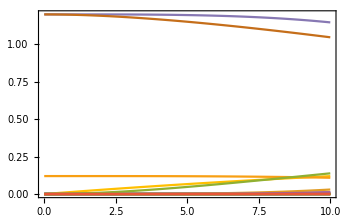

```mathematica
plotSimulation[conc, PlotFunction-> Plot]
```

```mathematica
glyc=ExampleData[{"Toolbox","Glycolysis"}]
```

## Get rate laws values at t=0

```mathematica
modelList[[1]]["Stoichiometry"]
```

{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,-1,0,0,0,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,-1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0}}

```mathematica
ic=#[[1]][0]-> #[[2]]&/@stripUnits[modelList[[2]]["InitialConditions"]];
nRates=Length[modelList[[1]]["Rates"]];
rateSub = {};
Table[
rateTemp = modelList[[1]]["Rates"][[i]];
rateSubTemp=rateTemp/. t-> 0/.stripUnits@modelList[[2]]["Parameters"]/.stripUnits@ic;
AppendTo[rateSub, {rateTemp, rateSubTemp}];,
{i, 1, nRates}];
```

```mathematica
rateSub//TableForm
```

Volume_c (-k_ENO1^⟵ (ENO^c&(2pg)^c)_^[t]+k_ENO1^⟶ (ENO^c)_^[t] (2pg)^c[t]) | 2.68687×10^-7
Volume_c (k_ENO2^⟶ (ENO^c&pep^c)_^[t]-k_ENO2^⟵ (ENO^c)_^[t] pep^c[t]) | 2.68862×10^-7
Volume_c (k_ENO3^⟶ (ENO^c&(2pg)^c)_^[t]-k_ENO3^⟵ (ENO^c&pep^c)_^[t]) | 2.68687×10^-7
Volume_c (-k_FBA11^⟵ (FBA1^c&fdp^c)_^[t]+k_FBA11^⟶ (FBA1^c)_^[t] fdp^c[t]) | 1.6657×10^-13
Volume_c (k_FBA12^⟶ (FBA1^c&g3p^c)_^[t]-k_FBA12^⟵ (FBA1^c)_^[t] g3p^c[t]) | 1.6657×10^-13
Volume_c (k_FBA13^⟶ (FBA1^c&fdp^c)_^[t]-k_FBA13^⟵ (FBA1^c&g3p^c&dhap^c)_^[t]) | 1.6657×10^-13
Volume_c (k_FBA14^⟶ (FBA1^c&g3p^c&dhap^c)_^[t]-k_FBA14^⟵ (FBA1^c&g3p^c)_^[t] dhap^c[t]) | 1.66533×10^-13
Volume_c (-k_GAPD1^⟵ (GAPD^c&nad^c)_^[t]+k_GAPD1^⟶ (GAPD^c)_^[t] nad^c[t]) | -0.00369858
Volume_c (k_GAPD2^⟶ (GAPD^c&(13dpg)^c)_^[t]-k_GAPD2^⟵ (GAPD^c)_^[t] (13dpg)^c[t]) | -0.00369858
Volume_c (-k_GAPD3^⟵ (GAPD^c&nad^c&g3p^c)_^[t]+k_GAPD3^⟶ (GAPD^c&nad^c)_^[t] g3p^c[t]) | -0.00369858
Volume_c (k_GAPD4^⟶ (GAPD^c&(13dpg)^c&nadh^c)_^[t]-k_GAPD4^⟵ (GAPD^c&(13dpg)^c)_^[t] nadh^c[t]) | -0.00369858
Volume_c (-k_GAPD5^⟵ (GAPD^c&nad^c&g3p^c&pi^c)_^[t]+k_GAPD5^⟶ (GAPD^c&nad^c&g3p^c)_^[t] pi^c[t]) | -0.00369858
Volume_c (-k_GAPD6^⟵ (GAPD^c&(13dpg)^c&nadh^c)_^[t]+k_GAPD6^⟶ (GAPD^c&nad^c&g3p^c&pi^c)_^[t]) | -0.00369858
Volume_c (-k_PGMd1^⟵ (PGMd^c&(2pg)^c)_^[t]+k_PGMd1^⟶ (PGMd^c)_^[t] (2pg)^c[t]) | 1.25216×10^-6
Volume_c (k_PGMd2^⟶ (PGMd^c&(3pg)^c)_^[t]-k_PGMd2^⟵ (PGMd^c)_^[t] (3pg)^c[t]) | 1.25216×10^-6
Volume_c (k_PGMd3^⟶ (PGMd^c&(2pg)^c)_^[t]-k_PGMd3^⟵ (PGMd^c&(3pg)^c)_^[t]) | 1.25216×10^-6
Volume_c (-k_PGMi1^⟵ (PGMi^c&(2pg)^c)_^[t]+k_PGMi1^⟶ (PGMi^c)_^[t] (2pg)^c[t]) | 0.000111006
Volume_c (k_PGMi2^⟶ (PGMi^c&(3pg)^c)_^[t]-k_PGMi2^⟵ (PGMi^c)_^[t] (3pg)^c[t]) | 0.000111006
Volume_c (k_PGMi3^⟶ (PGMi^c&(2pg)^c)_^[t]-k_PGMi3^⟵ (PGMi^c&(3pg)^c)_^[t]) | 0.000111006
Volume_c (-k_PYK11^⟵ (PYK1^c&pep^c)_^[t]+k_PYK11^⟶ (PYK1^c)_^[t] pep^c[t]) | -7.27596×10^-10
Volume_c (-k_PYK12^⟵ (PYK1^c&adp^c)_^[t]+k_PYK12^⟶ (PYK1^c)_^[t] adp^c[t]) | -7.29415×10^-10
Volume_c (k_PYK13^⟶ (PYK1^c&atp^c)_^[t]-k_PYK13^⟵ (PYK1^c)_^[t] atp^c[t]) | -1.411×10^-9
Volume_c (k_PYK14^⟶ (PYK1^c&pyr^c)_^[t]-k_PYK14^⟵ (PYK1^c)_^[t] pyr^c[t]) | -3.3289×10^-11
Volume_c (-k_PYK15^⟵ (PYK1^c&pep^c&adp^c)_^[t]+k_PYK15^⟶ (PYK1^c&adp^c)_^[t] pep^c[t]) | -7.29726×10^-10
Volume_c (-k_PYK16^⟵ (PYK1^c&pep^c&adp^c)_^[t]+k_PYK16^⟶ (PYK1^c&pep^c)_^[t] adp^c[t]) | -7.17259×10^-10
Volume_c (k_PYK17^⟶ (PYK1^c&pyr^c&atp^c)_^[t]-k_PYK17^⟵ (PYK1^c&atp^c)_^[t] pyr^c[t]) | -1.411×10^-9
Volume_c (k_PYK18^⟶ (PYK1^c&pyr^c&atp^c)_^[t]-k_PYK18^⟵ (PYK1^c&pyr^c)_^[t] atp^c[t]) | -9.27766×10^-11
Volume_c (k_PYK19^⟶ (PYK1^c&pep^c&adp^c)_^[t]-k_PYK19^⟵ (PYK1^c&pyr^c&atp^c)_^[t]) | -1.44417×10^-9
Volume_c (-k_PYK21^⟵ (PYK2^c&pep^c)_^[t]+k_PYK21^⟶ (PYK2^c)_^[t] pep^c[t]) | 5.81611×10^-26
Volume_c (-k_PYK22^⟵ (PYK2^c&adp^c)_^[t]+k_PYK22^⟶ (PYK2^c)_^[t] adp^c[t]) | 8.66448×10^-19
Volume_c (k_PYK23^⟶ (PYK2^c&atp^c)_^[t]-k_PYK23^⟵ (PYK2^c)_^[t] atp^c[t]) | 0.00262208
Volume_c (k_PYK24^⟶ (PYK2^c&pyr^c)_^[t]-k_PYK24^⟵ (PYK2^c)_^[t] pyr^c[t]) | 0.0042851
Volume_c (-k_PYK25^⟵ (PYK2^c&pep^c&adp^c)_^[t]+k_PYK25^⟶ (PYK2^c&adp^c)_^[t] pep^c[t]) | 8.66448×10^-19
Volume_c (-k_PYK26^⟵ (PYK2^c&pep^c&adp^c)_^[t]+k_PYK26^⟶ (PYK2^c&pep^c)_^[t] adp^c[t]) | 5.0851×10^-26
Volume_c (k_PYK27^⟶ (PYK2^c&pyr^c&atp^c)_^[t]-k_PYK27^⟵ (PYK2^c&atp^c)_^[t] pyr^c[t]) | -0.00597987
Volume_c (k_PYK28^⟶ (PYK2^c&pyr^c&atp^c)_^[t]-k_PYK28^⟵ (PYK2^c&pyr^c)_^[t] atp^c[t]) | -5.11501×10^7
Volume_c (k_PYK29^⟶ (PYK2^c&pep^c&adp^c)_^[t]-k_PYK29^⟵ (PYK2^c&pyr^c&atp^c)_^[t]) | 8.66448×10^-19
Volume_c k_PGK^⟶ (-((13dpg)^c[t] adp^c[t])/K_PGK+(3pg)^c[t] atp^c[t]) | -3.82882×10^-6
Volume_c k_TPI^⟶ (dhap^c[t]-g3p^c[t]/K_TPI) | 1.8728×10^-6

```mathematica
ic=#[[1]][0]-> #[[2]]&/@stripUnits[modelPERC["InitialConditions"]];
nRates=Length[modelPERC["Rates"]];
rateSubPERCs = {};
Table[
rateTemp = modelPERC["Rates"][[i]];
rateSubTemp=rateTemp/. t-> 0/.stripUnits@modelPERC["Parameters"]/.stripUnits@ic;
AppendTo[rateSubPERCs, {rateTemp, rateSubTemp}];,
{i, 1, nRates}];
```

```mathematica
rateSubPERCs//TableForm
```

Volume_c k_FBA1^⟶ (fdp^c[t]-(dhap^c[t] g3p^c[t])/K_FBA1) | 1.8728×10^-6
Volume_c k_TPI^⟶ (dhap^c[t]-g3p^c[t]/K_TPI) | 1.8728×10^-6
Volume_c k_GAPD^⟶ (-((13dpg)^c[t] nadh^c[t])/K_GAPD+g3p^c[t] nad^c[t] pi^c[t]) | 3.82881×10^-6
Volume_c k_PGK^⟶ (-((13dpg)^c[t] adp^c[t])/K_PGK+(3pg)^c[t] atp^c[t]) | -3.82881×10^-6
Volume_c k_PGMd^⟶ ((2pg)^c[t]-(3pg)^c[t]/K_PGMd) | -3.60441×10^-6
Volume_c k_ENO^⟶ ((2pg)^c[t]-pep^c[t]/K_ENO) | 3.60441×10^-6
Volume_c k_PYK1^⟶ (adp^c[t] pep^c[t]-(atp^c[t] pyr^c[t])/K_PYK1) | 8.91153×10^-7

## Simulations

```mathematica
Import["plot_functions.m" ]
```

### Simulate enzyme modules model

```mathematica
<<"modelsENO.mx"
```

```mathematica
setFluxes [modelList_,modelNum_]:=Module[{model,sub, fluxes},
model=modelList[[modelNum ]];
sub=Map[#-> #[t]&,Keys@modelList[[modelNum]]["InitialConditions"]];
initCond=stripUnits@modelList[[modelNum]]["InitialConditions"]/.sub;
fluxes=stripUnits@modelList[[modelNum]]["Rates"]/.initCond/.stripUnits@modelList[[modelNum]]["Parameters"];
(*modelList[[modelNum]]["Stoichiometry"].fluxes*)
model=addReactions[modelList[[modelNum]],{reaction["EX_2pg[c]",{},{metabolite["2pg","c"]},{1},False], reaction["EX_pep[c]",{metabolite["pep","c"]},{},{1},False]}];
updateCustomRateLaws[model,Thread[{Subscript[v, EX_2pg[c]],Subscript[v, EX_pep[c]] }-> fluxes[[1]]]];
Return[model]];
```

```mathematica
modifiedModelList={};
Table[
model=setFluxes[modelList,i];
AppendTo[modifiedModelList,model];,
{i, 1,Length@modelList}];
```

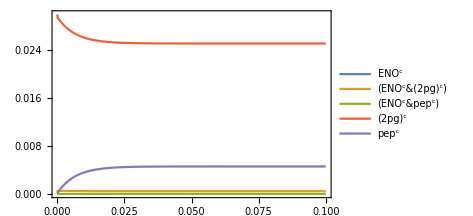

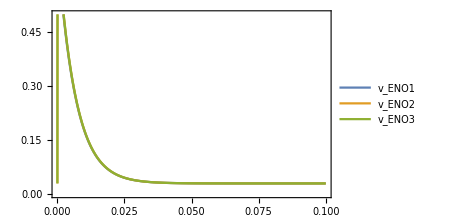

```mathematica
initCondList={(2pg)^c-> 0.03};
{conc, flux}=simulate[modifiedModelList[[1]],{t,0,0.1}, InitialConditions-> initCondList];
plotSimulation[conc,PlotFunction->Plot,PlotRange->{{0,0.1},{0,0.03}}, Legend-> True]
plotSimulation[FilterRules[flux,{Subscript[v, ENO1],Subscript[v, ENO2],Subscript[v, ENO3]}],PlotFunction-> Plot,PlotRange->{{0,0.1},{0,0.5}}, Legend-> True]
```

```mathematica
res=Map[Check[simulateModels[modifiedModelList[[#]],0.1,{(2pg)^c-> 0.03}],"err"]&,Range[1,100]];
```

```mathematica
resWorking=Delete[res,Position[res,"err"]];
resConc=resWorking[[All,1]];
resFlux=resWorking[[All,2]];
```

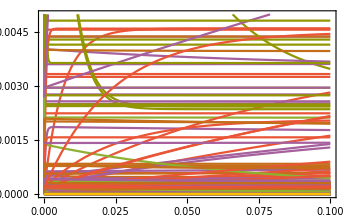

```mathematica
plotsConc=Map[plotSimulation[resConc[[#]], PlotFunction->Plot,PlotRange->{{0,0.1},{0,0.005}}]&,Range[1,100]];
Show[plotsConc,PlotRange->{{0,0.1},{0.,0.005}}]
```

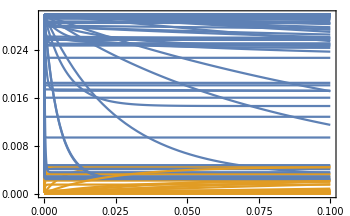

```mathematica
plotsConc=Map[plotSimulation[FilterRules[resConc[[#]],{(2pg)^c,pep^c}], PlotFunction->Plot,PlotRange->{{0,0.1},{0,0.03}}]&,Range[1,100]];
Show[plotsConc,PlotRange->{{0,0.1},{0.,0.03}}]
```

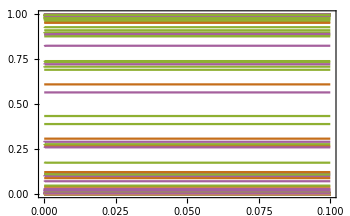

```mathematica
plotsConc=Map[plotSimulation[FilterRules[resConc[[#]],{(ENO^c)_^,(ENO^c&(2pg)^c)_^,(ENO^c&pep^c)_^}], PlotFunction->Plot,PlotRange->{{0,0.1},{0,1}}]&,Range[1,100]];
Show[plotsConc,PlotRange->{{0,0.1},{0.,1}}]
```

$Aborted

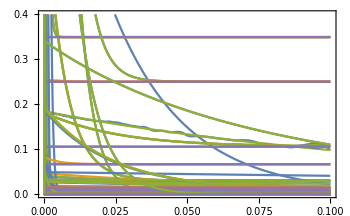

```mathematica
plotsFlux=Map[plotSimulation[FilterRules[resFlux,{Subscript[v, ENO1],Subscript[v, ENO2],Subscript[v, ENO3]}], PlotFunction->Plot,PlotRange->{{0,0.1},{0,0.4}}]&,Range[1,100]];
Show[plotsFlux,PlotRange->{{0,0.1},{0.,0.4}}]
```

### Min-max intervals plots

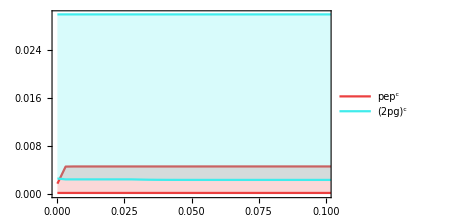

```mathematica
plotsConc2=MapThread[plotIntervalsConcs[resConc,#1,10, #2]&,{{pep^c,(2pg)^c},discreteColors[2]}];
Show[plotsConc2,PlotRange->{{0,0.1},{0,0.03}}]
```

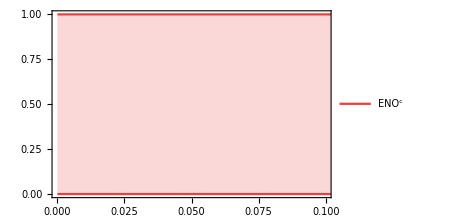

```mathematica
plotsConc3=MapThread[plotIntervalsConcs[resConc,#1,10, #2]&,{{(ENO^c)_^},discreteColors[1]}];
Show[plotsConc3,PlotRange->{{0,0.1},{0,1}}]
```

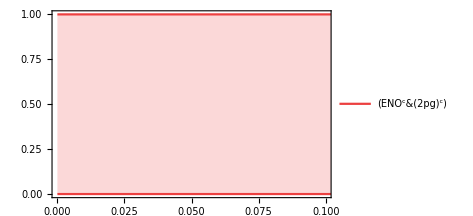

```mathematica
plotsConc4=MapThread[plotIntervalsConcs[resConc,#1,10, #2]&,{{(ENO^c&(2pg)^c)_^},discreteColors[1]}];
Show[plotsConc4,PlotRange->{{0,0.1},{0,1}}]
```

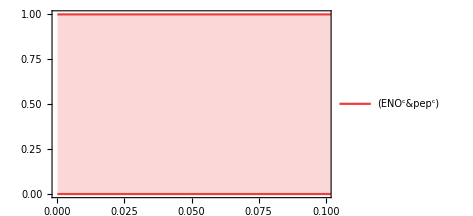

```mathematica
plotsConc3=MapThread[plotIntervalsConcs[resConc,#1,10, #2]&,{{(ENO^c&pep^c)_^},discreteColors[1]}];
Show[plotsConc3,PlotRange->{{0,0.1},{0,1}}]
```

### Flux plots

```mathematica
plotListFlux1=Map[
plotSimulation[resFlux[[#]],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 18],
			FrameLabel->{"Time (s)","Concentration (mol)"},
			PlotRangePadding->0,
			ImageSize->{600,400},
			If[#>(Length[resFlux]-1),
			Legend-> True,
			Legend-> False],
			PlotFunction->Plot]&, Range[1,2]];
```

```mathematica
Show[plotListFlux1,PlotRange-> {{0,10000},{-1,1}}]
```

### Metabolite time-courses for all models

```mathematica
Cases[modelList[[1]]["Species"],_metabolite]
```

{adp^c,atp^c,dhap^c,fdp^c,g3p^c,nad^c,nadh^c,pep^c,pi^c,pyr^c,(13dpg)^c,(2pg)^c,(3pg)^c}

```mathematica
Keys@resConc[[1]]
```

{(ENO^c)_^,(ENO^c&(2pg)^c)_^,(ENO^c&pep^c)_^,(FBA1^c)_^,(FBA1^c&fdp^c)_^,(FBA1^c&g3p^c)_^,(FBA1^c&g3p^c&dhap^c)_^,(GAPD^c)_^,(GAPD^c&(13dpg)^c)_^,(GAPD^c&nad^c)_^,(GAPD^c&(13dpg)^c&nadh^c)_^,(GAPD^c&nad^c&g3p^c)_^,(GAPD^c&nad^c&g3p^c&pi^c)_^,(PGMd^c)_^,(PGMd^c&(2pg)^c)_^,(PGMd^c&(3pg)^c)_^,(PGMi^c)_^,(PGMi^c&(2pg)^c)_^,(PGMi^c&(3pg)^c)_^,(13dpg)^c,(2pg)^c,(3pg)^c,adp^c,atp^c,dhap^c,fdp^c,g3p^c,nad^c,nadh^c,pep^c,pi^c}

```mathematica
plotList1=Map[plotSimulation[FilterRules[resConc[[#]],{fdp^c,dhap^c,g3p^c,(13dpg)^c,(3pg)^c,(2pg)^c,pep^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 20],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,
			ImageSize->{600,400},
			PlotStyle-> ColorData[97,"ColorList"],
			If[#>(Length[resWorking]-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{(13dpg)^c,(2pg)^c,(3pg)^c,dhap^c,fdp^c,g3p^c,pep^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,Length[resWorking]]];
```

```mathematica
plotList2=Map[plotSimulation[FilterRules[resConc[[#]],{adp^c,atp^c,pi^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 20],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,			
			ImageSize->{600,400},
			If[#>(Length[resWorking]-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{adp^c,atp^c,pi^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,Length[resWorking]]];
```

```mathematica
plotList3=Map[plotSimulation[FilterRules[resConc[[#]],{nad^c,nadh^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 20],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,
			ImageSize->{600,400},
			If[#>(Length[resWorking]-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{nad^c,nadh^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,Length[resWorking]]];
```

```mathematica
modelList[[1]]["BoundaryConditions"]
```

{atp^c,dhap^c,fdp^c,nadh^c,pep^c}

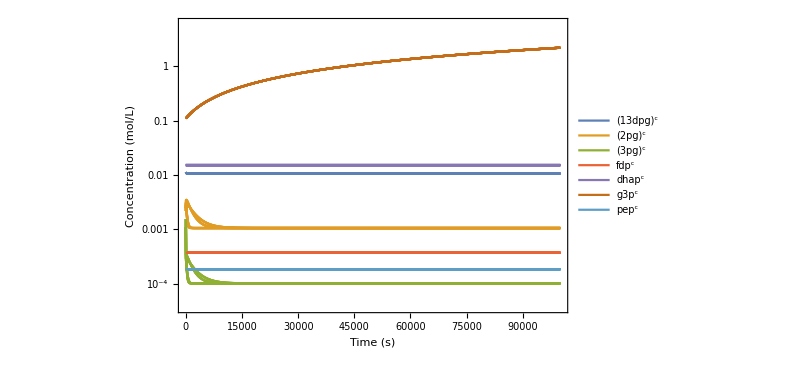

```mathematica
Show[plotList1[[17;;32]]]
```

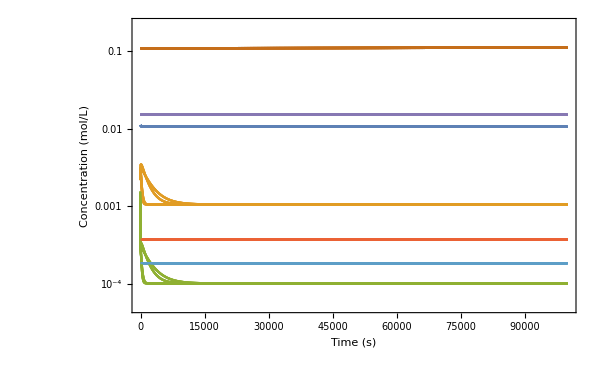

```mathematica
Show[plotList1[[1;;16]]]
```

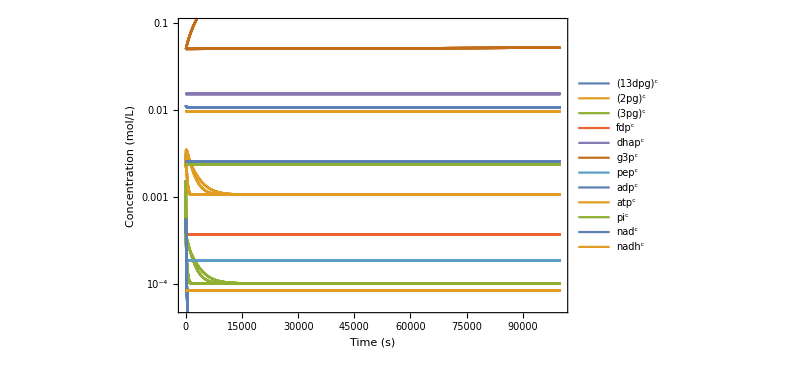

```mathematica
plot=Show[Flatten@{plotList1,plotList2,plotList3}] (*g3p=0.05*)
```

```mathematica
Export["dynamics_g3p005.pdf",plot,"PDF"];
```

```mathematica
plot=Show[Flatten@{plotList1,plotList2,plotList3}] (*g3p=0.11*)
```

```mathematica
plot=Show[Flatten@{plotList1,plotList2,plotList3}] (*g3p=0.11*)
```

```mathematica
Export["dynamics_g3p011_font20.pdf",plot,"PDF"];
```

```mathematica
plot=Show[Flatten@{plotList1,plotList2,plotList3}] (*no tweaks*)
```

```mathematica
Export["dynamics_noTweaks_font24.pdf",plot,"PDF"];
```

```mathematica
modelT["InitialConditions"]
```

### Simulate perturbations

```mathematica
modelT=modelList[[1]];
```

```mathematica
modelListSS={};
Table[
initCond=resConc[[i]]/.t-> 100000;
modelT=modelList[[i]];
updateInitialConditions[modelT, initCond];
AppendTo[modelListSS,modelT];,
{i,1,Length[modelList]}]
```

```mathematica
<<"modelsNoPYKSS.mx"
```

```mathematica
Import["plot_functions.m"]
```

```mathematica
resSS=Map[Check[simulateModels[modelListSS[[#]], #,60],"err"]&,Range[1,32]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

```mathematica
resWorkingSS=Delete[resSS,Position[resSS,"err"]];
```

```mathematica
DumpSave["resWorkingT100000g3p011SS.mx",resWorkingSS];
```

```mathematica
<<"resWorkingT100000g3p011SS.mx"
```

```mathematica
resConcSS=resWorkingSS[[All,1]];
resFluxSS=resWorkingSS[[All,2]];
```

```mathematica
Keys@resConcSS[[1]]
```

{(ENO^c)_^,(ENO^c&(2pg)^c)_^,(ENO^c&pep^c)_^,(FBA1^c)_^,(FBA1^c&fdp^c)_^,(FBA1^c&g3p^c)_^,(FBA1^c&g3p^c&dhap^c)_^,(GAPD^c)_^,(GAPD^c&(13dpg)^c)_^,(GAPD^c&nad^c)_^,(GAPD^c&(13dpg)^c&nadh^c)_^,(GAPD^c&nad^c&g3p^c)_^,(GAPD^c&nad^c&g3p^c&pi^c)_^,(PGMd^c)_^,(PGMd^c&(2pg)^c)_^,(PGMd^c&(3pg)^c)_^,(PGMi^c)_^,(PGMi^c&(2pg)^c)_^,(PGMi^c&(3pg)^c)_^,(13dpg)^c,(2pg)^c,(3pg)^c,adp^c,atp^c,dhap^c,fdp^c,g3p^c,nad^c,nadh^c,pep^c,pi^c}

```mathematica
plotList1=Map[plotSimulation[FilterRules[resConcSS[[#]],{fdp^c,dhap^c,g3p^c,(13dpg)^c,(3pg)^c,(2pg)^c,pep^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 24],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,
			ImageSize->{600,400},
			PlotStyle-> ColorData[97,"ColorList"],
			If[#>(16-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{(13dpg)^c,(2pg)^c,(3pg)^c,dhap^c,fdp^c,g3p^c,pep^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,16]];
```

```mathematica
plotList2=Map[plotSimulation[FilterRules[resConcSS[[#]],{adp^c,atp^c,pi^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 24],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,			
			ImageSize->{600,400},
			If[#>(16-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{adp^c,atp^c,pi^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,16]];
```

```mathematica
plotList3=Map[plotSimulation[FilterRules[resConcSS[[#]],{nad^c,nadh^c}],
			FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 24],
			FrameLabel->{"Time (s)","Concentration (mol/L)"},
			PlotRangePadding->0,
			ImageSize->{600,400},
			If[#>(16-1),
				PlotLegends-> LineLegend[ColorData[97,"ColorList"],{nad^c,nadh^c},
			    LabelStyle->{FontFamily->"Arial",FontSize->18}],##&[]],
			PlotFunction->LogPlot]&, Range[1,16]];
```

```mathematica
plot=Show[Flatten@{plotList1,plotList2,plotList3}]
```

```mathematica
Export["dynamics_g3p011SSadp005_font24.pdf",plot,"PDF"];
```

## Calculate Jacobian

### PERC model

```mathematica
model=modifiedModelList[[5]];
jacobian=getJacobian[model]/.stripUnits[model["InitialConditions"]]/.stripUnits[model["Parameters"]];
Sort[Re@Eigenvalues[jacobian]]
```

{-267417.,-28750.,-149.468,8.92901×10^-13,3.38371×10^-12}

```mathematica
jacobian=getJacobian[modelList[[80]]]/.stripUnits[modelList[[80]]["InitialConditions"]]/.stripUnits[modelList[[80]]["Parameters"]];
Sort[Re@Eigenvalues[jacobian]]
```

{-9660.66,-5.45235,-0.0928367,-1.45866×10^-14,-1.45866×10^-14}

```mathematica
modelList[[17]]["Stoichiometry"]
```

{{-1,1,0},{1,0,-1},{-1,0,0},{0,1,0},{0,-1,1}}

```mathematica
modelList[[1]]["Stoichiometry"].(Values[resFlux[[1]]/.t-> 0])
```

{1.33124×10^-15,-1.33097×10^-15,-1.71307×10^-12,1.71441×10^-12,-2.72762×10^-19}

```mathematica
modelList[[17]]["Stoichiometry"].(Values[resFlux[[17]]/.t-> 10])
```

{0.,0.,0.,0.,0.}

```mathematica
modelList[[17]]["Rates"][[1]][[2]]
```

-k_ENO1^⟵ (ENO^c&(2pg)^c)_^[t]+k_ENO1^⟶ (ENO^c)_^[t] (2pg)^c[t]

```mathematica
Map[Head@#&, modelList[[17]]["Rates"]]
```

{Times,Times,Times}

```mathematica
modelList[[modelNum]]
```

### enzyme modules model

```mathematica
jacobian=getJacobian[modelList[[100]]]/.stripUnits[modelList[[100]]["InitialConditions"]]/.stripUnits[modelList[[100]]["Parameters"]];Sort[Re@Eigenvalues[jacobian]]
```

{-1.46269×10^9,-1.34443×10^9,-9.9417×10^8,-9.79118×10^8,-9.30568×10^8,-8.87224×10^8,-8.68397×10^8,-8.66307×10^8,-2.63429×10^8,-2.63347×10^8,-1.6206×10^8,-1.57523×10^7,-6.41073×10^6,-3.24668×10^6,-3.16648×10^6,-990688.,-989044.,-378523.,-302094.,-186385.,-114065.,-70698.4,-213.29,-173.987,-149.141,-102.787,-7.30709,-0.292479,-0.000472573,-0.000472573,-0.0000191066,-4.17859×10^-8,-2.03806×10^-8,-3.59564×10^-9,-3.59564×10^-9,-2.47058×10^-9,-2.47058×10^-9,-1.628×10^-9,-5.9835×10^-10,-2.11731×10^-11,-2.11731×10^-11,3.19129×10^-15,1.86932×10^-9,3.20352×10^-9,1.39172×10^-8,1.39172×10^-8}

```mathematica
jacobian=getJacobian[modelList[[3]]]/.stripUnits[modelList[[3]]["InitialConditions"]]/.stripUnits[modelList[[3]]["Parameters"]];Sort[Re@Eigenvalues[jacobian]]
```

{-6.74875×10^8,-2.54496×10^6,-2.20156×10^6,-378523.,-301164.,-129679.,-70698.4,-149.141,-0.00725551,-0.0000191058,-1.04681×10^-8,-6.37141×10^-12,-2.34583×10^-41,-2.29405×10^-56,2.30405×10^-23,2.53328×10^-13,1.38621×10^-11,2.27252×10^-11,2.27252×10^-11,1.33108×10^-10}

```mathematica
posEigenvalues={};
Table[
jacobian=getJacobian[modelListSS[[i]]]/.stripUnits[modelListSS[[i]]["InitialConditions"]]/.stripUnits[modelListSS[[i]]["Parameters"]];eigenvalues=Sort[Re@Eigenvalues[jacobian]];
posEigTemp={};
Table[If[eigenvalues[[j]]> 0,
AppendTo[posEigTemp, eigenvalues[[j]]]];,
{j,1,Length[eigenvalues]}]
Print[posEigTemp];
AppendTo[posEigenvalues,posEigTemp];,
{i, 1, Length[modelListSS]}]
```

{1.06913×10^-12,3.02963×10^-10,1.13942×10^-9,9.20521×10^-8}

{2.63662×10^-35,2.49322×10^-14,2.25971×10^-10,2.16221×10^-8}

{5.14777×10^-22,2.38879×10^-12,4.2925×10^-10,7.62299×10^-9,1.65275×10^-8}

{1.90358×10^-21,8.54968×10^-12,1.43302×10^-11,4.08134×10^-11,2.30001×10^-9,5.69209×10^-9}

{6.39142×10^-22,1.8734×10^-18,2.7278×10^-11,4.05653×10^-10,2.79096×10^-9}

{6.23942×10^-14,4.49048×10^-11,4.49048×10^-11,4.36994×10^-10}

{4.56225×10^-15,4.79875×10^-12,3.0258×10^-11,1.25306×10^-8,3.40764×10^-8}

{7.71598×10^-20,1.49994×10^-14,2.76566×10^-11,1.24259×10^-10,1.24259×10^-10,1.08668×10^-8}

{3.30725×10^-19,3.30725×10^-19,7.64524×10^-16,3.37624×10^-10,5.95337×10^-9,1.04746×10^-7}

{4.09867×10^-34,9.70409×10^-18,1.20023×10^-13,9.77747×10^-12,1.16424×10^-9,1.55068×10^-8}

{1.72185×10^-36,5.76176×10^-19,1.62309×10^-15,1.09822×10^-14,5.17549×10^-10,6.55054×10^-9,1.11582×10^-8,1.11582×10^-8}

{3.75703×10^-37,1.73543×10^-17,1.49725×10^-10,1.21225×10^-8}

{7.77827×10^-19,1.59901×10^-16,2.92891×10^-10,2.92182×10^-8,6.6887×10^-8}

{1.8016×10^-15,4.0488×10^-8}

{3.87847×10^-37,8.53533×10^-9,8.53533×10^-9}

{7.56612×10^-20,3.60036×10^-17,1.53038×10^-15,1.53038×10^-15,6.20388×10^-10}

{2.95513×10^-18,1.12009×10^-14,2.10957×10^-11,3.17814×10^-10,2.02625×10^-9,3.32248×10^-8}

{2.13263×10^-19,3.95964×10^-15,3.08178×10^-13,2.12646×10^-8}

{3.00927×10^-36,3.46576×10^-20,2.92171×10^-14,4.44003×10^-12,4.44003×10^-12,7.07372×10^-11,7.13796×10^-10,8.11313×10^-9}

{5.75783×10^-19,2.41379×10^-14,1.05485×10^-11,1.05485×10^-11,2.75484×10^-10,1.06345×10^-9,1.01036×10^-8}

{7.7409×10^-17,2.72994×10^-10,3.35546×10^-9,4.57639×10^-8,4.57639×10^-8}

{7.70372×10^-34,7.59855×10^-18,1.82397×10^-15,1.82397×10^-15,6.44952×10^-13,6.44952×10^-13,7.57082×10^-11,2.77367×10^-10,2.07165×10^-9,2.9812×10^-8}

{1.13616×10^-19,4.32735×10^-11,2.45492×10^-8,2.45492×10^-8}

{5.39383×10^-19,6.94529×10^-13,6.94529×10^-13,1.73237×10^-11,1.96755×10^-8,2.02042×10^-8,2.3508×10^-8}

{3.51049×10^-10,3.51049×10^-10,8.77743×10^-8}

{1.23393×10^-33,3.85067×10^-17,1.17672×10^-13,8.57629×10^-13,1.41397×10^-10,4.21239×10^-8}

{3.68302×10^-16,1.16303×10^-13,1.16303×10^-13,2.01461×10^-10,2.48705×10^-8,2.48705×10^-8,3.58832×10^-8}

{1.2326×10^-32,3.45784×10^-9}

{2.69115×10^-14,1.07386×10^-12,7.23087×10^-11,7.23087×10^-11,2.36877×10^-10,2.41445×10^-9,6.08724×10^-9,2.20932×10^-8,2.20932×10^-8}

{9.10121×10^-33,2.8428×10^-13,1.06842×10^-12,6.80034×10^-9,6.80034×10^-9}

{1.73971×10^-9,1.21167×10^-8,3.18607×10^-8,4.69548×10^-8,4.69548×10^-8}

{4.04322×10^-35,1.23058×10^-14,1.23058×10^-14,8.6078×10^-13,4.75751×10^-11,4.75751×10^-11,1.433×10^-8,5.40973×10^-8}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Max[Flatten@posEigenvalues]
```

1.04746×10^-7

```mathematica
posEigenvalues={};
Table[
jacobian=getJacobian[modelList[[i]]]/.stripUnits[modelList[[i]]["InitialConditions"]]/.stripUnits[modelList[[i]]["Parameters"]];eigenvalues=Sort[Re@Eigenvalues[jacobian]];
posEigTemp={};
Table[If[eigenvalues[[j]]> 0,
AppendTo[posEigTemp, eigenvalues[[j]]]];,
{j,1,Length[eigenvalues]}]
AppendTo[posEigenvalues,posEigTemp];,
{i, 1, Length[modelList]}]
```

{6.01853×10^-36,1.36775×10^-14,2.47407×10^-11,6.13949×10^-11,1.95905×10^-10,3.18177×10^-10,8.87318×10^-8}

{5.36613×10^-36,9.36889×10^-23,3.60295×10^-18,2.31426×10^-16,2.23555×10^-11,4.57313×10^-11,2.86263×10^-9,2.8436×10^-8}

{3.31993×10^-35,4.03991×10^-25,2.15793×10^-14,4.94816×10^-9}

{4.14837×10^-37,3.18206×10^-23,1.25393×10^-20,1.25608×10^-15,2.70422×10^-12,2.70422×10^-12,1.70914×10^-9,2.00717×10^-8}

{1.01627×10^-21,8.17137×10^-12,8.17137×10^-12,1.64952×10^-9,2.91048×10^-9}

{5.37014×10^-21,6.04052×10^-13,2.13952×10^-12,3.70634×10^-12,1.05993×10^-11,2.85046×10^-9,2.85046×10^-9,2.14171×10^-8}

{3.28404×10^-36,1.59513×10^-23,1.25172×10^-14,5.62465×10^-12,5.62465×10^-12,9.44203×10^-11,9.93042×10^-10,2.7918×10^-9,3.73677×10^-8,3.73677×10^-8}

{1.00679×10^-36,4.79037×10^-25,9.07431×10^-20,6.84127×10^-13,6.84127×10^-13,1.97396×10^-11,2.22077×10^-10,5.24685×10^-10,2.24007×10^-9,6.12371×10^-9}

{3.62487×10^-22,1.3984×10^-18,1.86172×10^-16,9.03948×10^-10,9.49558×10^-9,4.18865×10^-8,2.05756×10^-7}

{1.35534×10^-11,3.83193×10^-9,3.83193×10^-9,8.26644×10^-8}

{7.15145×10^-16,3.62527×10^-9,1.01111×10^-8,1.24971×10^-8}

{3.41078×10^-17,1.88708×10^-15,1.77826×10^-11,7.29773×10^-9,2.65002×10^-8}

{1.69959×10^-9,2.25863×10^-8}

{3.97813×10^-18,3.80051×10^-16,5.70689×10^-12,1.00532×10^-8,1.00532×10^-8}

{1.01277×10^-15,3.21171×10^-15,1.3111×10^-9,1.3111×10^-9,2.70538×10^-8}

{1.27529×10^-20,5.13105×10^-19,4.39401×10^-9,1.27797×10^-8,4.17106×10^-8}

{7.68643×10^-15,2.6424×10^-11,3.83771×10^-11,4.9531×10^-9}

{4.23278×10^-25,4.90417×10^-11,6.64524×10^-9,4.21445×10^-8}

{6.71744×10^-24,1.36122×10^-14,9.63679×10^-13,3.47692×10^-11,7.58759×10^-11,2.74412×10^-9,2.74412×10^-9,3.85428×10^-8}

{1.21311×10^-35,4.81928×10^-12,4.81928×10^-12,1.71134×10^-11,1.68532×10^-9,1.32569×10^-8}

{3.76158×10^-37,6.22726×10^-21,4.29283×10^-12,3.33433×10^-8,3.33433×10^-8}

{1.19527×10^-12,4.99969×10^-12,1.95932×10^-11,1.95932×10^-11,7.89199×10^-11,2.09549×10^-8,4.01953×10^-8}

{5.8073×10^-36,3.17434×10^-15,1.52149×10^-11,3.50924×10^-11,7.28671×10^-9}

{2.98576×10^-36,1.94361×10^-14,9.76093×10^-14,9.76093×10^-14,1.96011×10^-12,5.43281×10^-10,2.31791×10^-8}

{2.82119×10^-37,3.78924×10^-13,8.64431×10^-11,1.66651×10^-9,1.8448×10^-8,2.45738×10^-8,4.1193×10^-8,1.53948×10^-7}

{4.58179×10^-20,8.56329×10^-17,1.83441×10^-13,1.38267×10^-11,1.38319×10^-10,1.84402×10^-8,1.84402×10^-8}

{5.51072×10^-34,3.52845×10^-21,1.06196×10^-9,2.83211×10^-9,8.1922×10^-9,3.41589×10^-8,5.07614×10^-8}

{7.8793×10^-37,1.01932×10^-13,1.08686×10^-10,1.62371×10^-9,1.10868×10^-8,1.91126×10^-8}

{1.2185×10^-18,3.53975×10^-10,7.77954×10^-9}

{1.10027×10^-18,1.25095×10^-16,8.14983×10^-14,3.38484×10^-11,1.79164×10^-8,4.0086×10^-8}

{7.52316×10^-37,4.53425×10^-20,3.05199×10^-13,5.94433×10^-10,4.769×10^-9,1.91833×10^-8,4.1062×10^-8}

{2.94085×10^-36,7.79133×10^-19,4.83701×10^-10,1.69811×10^-9,6.19625×10^-9}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Max[posEigenvalues]
```

2.05756×10^-7

{-5.89237×10^19,-2.32843×10^9,-1.98201×10^9,-1.58621×10^9,-9.91522×10^8,-8.85438×10^8,-8.42578×10^8,-7.82747×10^8,-6.78154×10^8,-1.44433×10^8,-9.30627×10^7,-9.25006×10^7,-5.54016×10^7,-4.78465×10^6,-1.08131×10^6,-697660.,-621779.,-435386.,-57282.1,-37338.8,-35929.5,-13537.,-880.871,-880.867,-37.5767,-0.0696991,-0.0243479,-0.000833561,-0.000465024,-0.0000540453,-9.15583×10^-6,-9.15583×10^-6,-2.72289×10^-6,-7.48247×10^-7,-1.6275×10^-8,-3.38739×10^-9,-1.45691×10^-10,-1.45691×10^-10,2.22607×10^-10,6.53495×10^-8,2.75306×10^-7,2.75306×10^-7,7.07935×10^-6,0.000307616,0.000307616,0.0626673}

## Disequilibrium constants

### For generalized reactions only

```mathematica
reactionsPERC={"FBA1: fdp[c] <=> g3p[c] + dhap[c]","GAPD: nad[c] + g3p[c] + pi[c] <=> 13dpg[c] + nadh[c]","PGK: 3pg[c] + atp[c] <=> 13dpg[c] + adp[c]","PGMd: 2pg[c] <=> 3pg[c]","ENO: 2pg[c] <=> pep[c]","PYK1: adp[c] + pep[c] <=> atp[c] + pyr[c]"};
reactionsPERC=str2mass/@reactionsPERC;
```

```mathematica
simpleModel=constructModel[reactionsPERC];
```

```mathematica
getDisequilibriumRatios[simpleModel]
```

{(dhap^c g3p^c)/(K_FBA1 fdp^c),((13dpg)^c nadh^c)/(K_GAPD g3p^c nad^c pi^c),((13dpg)^c adp^c)/(K_PGK (3pg)^c atp^c),(3pg)^c/(K_PGMd (2pg)^c),pep^c/(K_ENO (2pg)^c),(atp^c pyr^c)/(K_PYK1 adp^c pep^c)}

```mathematica
modelT=modelListSS[[1]];
```

```mathematica
newInitCond={adp^c->0.05Mole Liter^-1};
updateInitialConditions[modelT,newInitCond];
```

```mathematica
(* no changes*)
disEqValues=getDisequilibriumRatios[simpleModel]/.modelT["InitialConditions"]/.modelListSS[[1]]["Parameters"];MapThread[getID[#1]-> #2&,{simpleModel["Reactions"],disEqValues}]//TableForm
```

FBA1→6.58805 Liter Mole^-1
GAPD→0.876776
PGK→1.
PGMd→0.00913095
ENO→0.0305318
PYK1→2.70835 Mole Liter^-1

```mathematica
(* adp(0) = 0.05*)
disEqValues=getDisequilibriumRatios[simpleModel]/.modelT["InitialConditions"]/.modelListSS[[1]]["Parameters"];MapThread[getID[#1]-> #2&,{simpleModel["Reactions"],disEqValues}]//TableForm
```

FBA1→6.58805 Liter Mole^-1
GAPD→0.876776
PGK→929113. Mole Liter^-1
PGMd→0.00913095
ENO→0.0305318
PYK1→2.91499×10^-6

```mathematica
modelT=modelList[[1]];
```

```mathematica
newInitCond={g3p^c->0.11Mole Liter^-1};
```

```mathematica
newInitCond={g3p^c->0.05Mole Liter^-1};
```

```mathematica
newInitCond={(2pg)^c->0.0001Mole Liter^-1};
```

```mathematica
updateInitialConditions[modelT,newInitCond];
```

```mathematica
(* no tweaks*)
disEqValues=getDisequilibriumRatios[simpleModel]/.modelT["InitialConditions"]/.modelList[[1]]["Parameters"];MapThread[getID[#1]-> #2&,{simpleModel["Reactions"],disEqValues}]//TableForm
```

FBA1→0.0246061
GAPD→247.018 Liter Mole^-1
PGK→709.21
PGMd→0.0675834
ENO→0.0147689
PYK1→0.000262612

```mathematica
(* g3p = 0.11*)
disEqValues=getDisequilibriumRatios[simpleModel]/.modelT["InitialConditions"]/.modelList[[1]]["Parameters"];MapThread[getID[#1]-> #2&,{simpleModel["Reactions"],disEqValues}]//TableForm
```

FBA1→6.49082
GAPD→0.936421 Liter Mole^-1
PGK→709.21
PGMd→0.0675834
ENO→0.0147689
PYK1→0.000262612

```mathematica
(* g3p = 0.05*)
disEqValues=getDisequilibriumRatios[simpleModel]/.modelT["InitialConditions"]/.modelList[[1]]["Parameters"];MapThread[getID[#1]-> #2&,{simpleModel["Reactions"],disEqValues}]//TableForm
```

FBA1→2.95037
GAPD→2.06013 Liter Mole^-1
PGK→709.21
PGMd→0.0675834
ENO→0.0147689
PYK1→0.000262612

### PERC model

```mathematica
getDisequilibriumRatios[modelPERC]
```

{(dhap^c g3p^c)/(K_FBA1 fdp^c),g3p^c/(K_TPI dhap^c),((13dpg)^c nadh^c)/(K_GAPD g3p^c nad^c pi^c),((13dpg)^c adp^c)/(K_PGK (3pg)^c atp^c),(3pg)^c/(K_PGMd (2pg)^c),pep^c/(K_ENO (2pg)^c),(atp^c pyr^c)/(K_PYK1 adp^c pep^c)}

```mathematica
disEqValues=getDisequilibriumRatios[modelPERC]/.modelPERC["InitialConditions"]/.modelPERC["Parameters"];MapThread[getID[#1]-> #2&,{modelPERC["Reactions"],disEqValues}]//TableForm
```

FBA1→0.0140981
TPI→10.2457
GAPD→8730.27
PGK→709.21
PGMd→0.128852
ENO→0.0162538
PYK1→0.000170007

### For each elementary reaction

```mathematica
rIds=getID[#]&/@model["Reactions"];
```

```mathematica
allEqConstsEq=Keq[#]-> rateconst[#,False]/rateconst[#,True]&/@rIds
```

{K_ENO1→k_ENO1^⟵/k_ENO1^⟶,K_ENO2→k_ENO2^⟵/k_ENO2^⟶,K_ENO3→k_ENO3^⟵/k_ENO3^⟶,K_FBA11→k_FBA11^⟵/k_FBA11^⟶,K_FBA12→k_FBA12^⟵/k_FBA12^⟶,K_FBA13→k_FBA13^⟵/k_FBA13^⟶,K_FBA14→k_FBA14^⟵/k_FBA14^⟶,K_GAPD1→k_GAPD1^⟵/k_GAPD1^⟶,K_GAPD2→k_GAPD2^⟵/k_GAPD2^⟶,K_GAPD3→k_GAPD3^⟵/k_GAPD3^⟶,K_GAPD4→k_GAPD4^⟵/k_GAPD4^⟶,K_GAPD5→k_GAPD5^⟵/k_GAPD5^⟶,K_GAPD6→k_GAPD6^⟵/k_GAPD6^⟶,K_PGMd1→k_PGMd1^⟵/k_PGMd1^⟶,K_PGMd2→k_PGMd2^⟵/k_PGMd2^⟶,K_PGMd3→k_PGMd3^⟵/k_PGMd3^⟶,K_PGMi1→k_PGMi1^⟵/k_PGMi1^⟶,K_PGMi2→k_PGMi2^⟵/k_PGMi2^⟶,K_PGMi3→k_PGMi3^⟵/k_PGMi3^⟶,K_PYK11→k_PYK11^⟵/k_PYK11^⟶,K_PYK12→k_PYK12^⟵/k_PYK12^⟶,K_PYK13→k_PYK13^⟵/k_PYK13^⟶,K_PYK14→k_PYK14^⟵/k_PYK14^⟶,K_PYK15→k_PYK15^⟵/k_PYK15^⟶,K_PYK16→k_PYK16^⟵/k_PYK16^⟶,K_PYK17→k_PYK17^⟵/k_PYK17^⟶,K_PYK18→k_PYK18^⟵/k_PYK18^⟶,K_PYK19→k_PYK19^⟵/k_PYK19^⟶,K_PYK21→k_PYK21^⟵/k_PYK21^⟶,K_PYK22→k_PYK22^⟵/k_PYK22^⟶,K_PYK23→k_PYK23^⟵/k_PYK23^⟶,K_PYK24→k_PYK24^⟵/k_PYK24^⟶,K_PYK25→k_PYK25^⟵/k_PYK25^⟶,K_PYK26→k_PYK26^⟵/k_PYK26^⟶,K_PYK27→k_PYK27^⟵/k_PYK27^⟶,K_PYK28→k_PYK28^⟵/k_PYK28^⟶,K_PYK29→k_PYK29^⟵/k_PYK29^⟶,K_PGK→k_PGK^⟵/k_PGK^⟶}

```mathematica
disRatios={};
boolDisRatios={};
Table[
allEqConsts=allEqConstsEq[[;;-2]]/.modelList[[i]]["Parameters"];
ratio=getDisequilibriumRatios[modelList[[i]]]/.modelList[[i]]["InitialConditions"]/.modelList[[i]]["Parameters"]/.allEqConsts;
AppendTo[disRatios,ratio];
(*boolRatio=Map[Check[If[#<1,1,Style[0,FontColor->Red]],Style["inf",FontColor->Purple]]&,stripUnits @ratio];*)
boolRatio=Map[Check[If[#<1,0,1],2]&,stripUnits @ratio];
AppendTo[boolDisRatios,boolRatio];,
{i, 1,64}];
```

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

```mathematica
Transpose@Join[{rIds}, disRatios]//TableForm
```

```mathematica
disRatioData=Transpose@Join[{rIds}, boolDisRatios]//TableForm
```

```mathematica
Export["disRatio.csv",disRatioData,"CSV"];
```

```mathematica
xticks=Transpose[{Range@64,Range[1,64]}];
yticks=Transpose[{Range@Length[rIds],rIds}];
yticks=MapAt[Rotate[#,Pi/2]&,yticks,{All,2}];
```

```mathematica
{#,#,{-0.003,0 }}&/@Range[1,14]
```

{{1,1,{-0.003,0}},{2,2,{-0.003,0}},{3,3,{-0.003,0}},{4,4,{-0.003,0}},{5,5,{-0.003,0}},{6,6,{-0.003,0}},{7,7,{-0.003,0}},{8,8,{-0.003,0}},{9,9,{-0.003,0}},{10,10,{-0.003,0}},{11,11,{-0.003,0}},{12,12,{-0.003,0}},{13,13,{-0.003,0}},{14,14,{-0.003,0}}}

```mathematica
ArrayPlot[boolDisRatios,
		Frame-> True,
		FrameTicks->{{#,#,{-0.003,0 }}&/@Range[1,64],{#[[1]],#[[2]],{-0.003,0}}&/@yticks},
		FrameStyle->Directive[Black,FontFamily->"Arial", FontSize-> 18],
		Mesh-> True,
		PlotRangePadding->0,
		PlotLegends->SwatchLegend[{White,Gray,Black},{"<1",">1","Nan"},LegendMarkerSize->20,
								LabelStyle->{FontFamily->"Arial",FontSize->18}]

		,ImageSize->{300,500},ImageMargins->0]
```